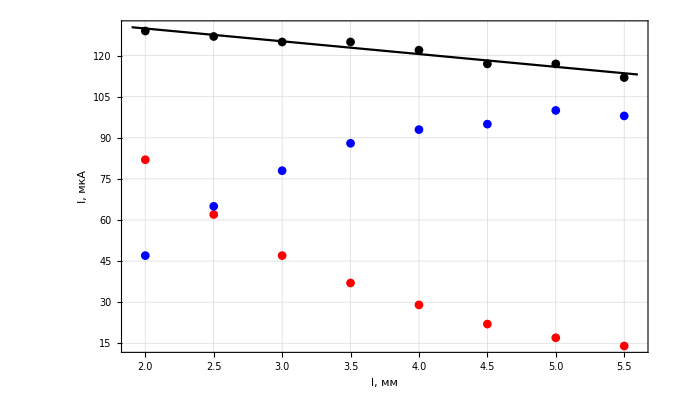

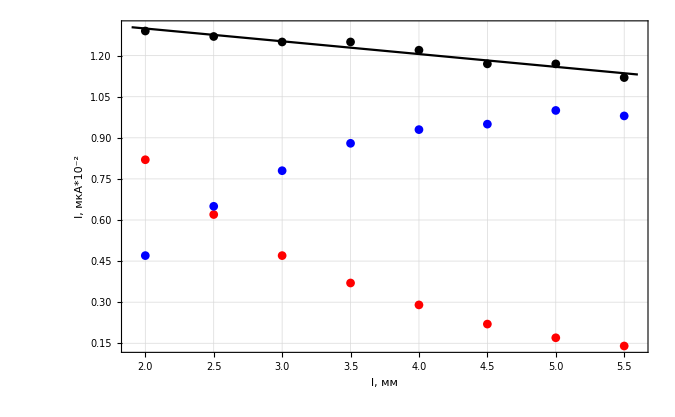

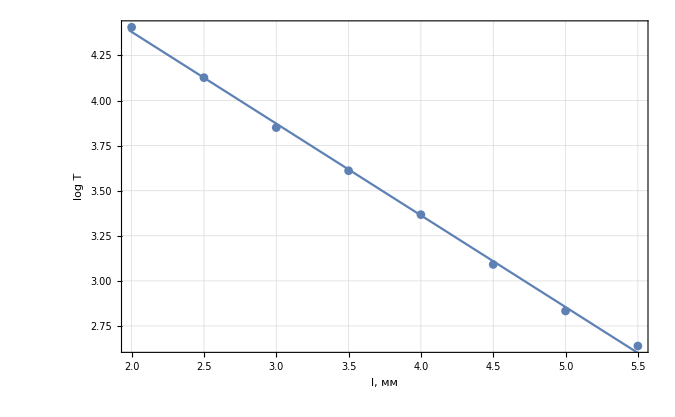

5.39821-0.508671 x

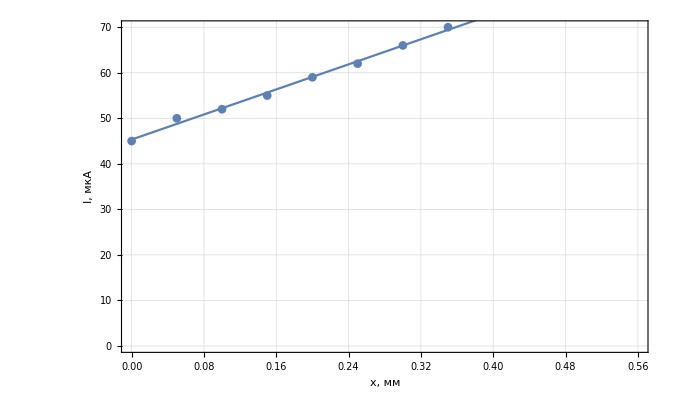

```mathematica
Needs["ErrorBarPlots`"];
xError = Table[0.005,8];

A={{2, 82}, {2.5, 62}, {3, 47}, {3.5, 37}, {4, 29}, {4.5, 22}, {5, 17}, {5.5, 14}};
B={{2, 47}, {2.5, 65}, {3, 78}, {3.5, 88}, {4, 93}, {4.5, 95}, {5, 100}, {5.5, 98}};
c=Array[0,{8,2}];
For[i = 1, i<9, i++,
c[[i,1]]=A[[i,1]];
c[[i,2]]=A[[i,2]]+B[[i,2]];
]
d=Array[0,{8,2}];
For[i=1,i<9,i++,
d[[i,1]]=A[[i,1]];
d[[i,2]]=Log[A[[i,2]]];
]
ApproxLine = LinearModelFit[c,x,x];
ApproxLine=ApproxLine["BestFit"];
Show[ListPlot[A, PlotStyle->Red, PlotTheme->"Detailed", GridLines->Automatic, PlotMarkers->Automatic],ListPlot[B,PlotStyle->Blue,PlotMarkers->Automatic],ListPlot[c,PlotStyle->Black,PlotMarkers->Automatic], Plot[ApproxLine,{x,1.9,5.6}, PlotStyle->Black],PlotRange->All,FrameLabel->{{RawBoxes[RowBox[{"I",","," ",RowBox[{"мкА"}]}]],None},{RawBoxes[RowBox[{"l",","," ","мм"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
For[i = 1, i<9, i++,
A[[i,2]]=A[[i,2]]/100;
B[[i,2]]=B[[i,2]]/100;
c[[i,1]]=A[[i,1]];
c[[i,2]]=A[[i,2]]+B[[i,2]];
]
ApproxLine = LinearModelFit[c,x,x];
ApproxLine=ApproxLine["BestFit"];
Show[ListPlot[A, PlotStyle->Red, PlotTheme->"Detailed", GridLines->Automatic, PlotMarkers->Automatic,Joined->False],ListPlot[B,PlotStyle->Blue,PlotMarkers->Automatic,Joined->False],ListPlot[c,PlotStyle->Black,PlotMarkers->Automatic,Joined->False],Plot[ApproxLine,{x,1.9,5.6}, PlotStyle->Black], PlotRange->All,FrameLabel->{{RawBoxes[RowBox[{"I",","," ",RowBox[{"мкА","*",SuperscriptBox["10",RowBox[{"-","2"}]]}]}]],None},{RawBoxes[RowBox[{"l",","," ","мм"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
ApproxLine2=LinearModelFit[d,x,x];
ApproxLine2=ApproxLine2["BestFit"];
Show[ListPlot[d,PlotTheme->"Detailed", GridLines->Automatic, PlotMarkers->Automatic],Plot[ApproxLine2,{x,1.98,5.6}],FrameLabel->{{HoldForm[log T],None},{RawBoxes[RowBox[{"l",","," ","мм"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
ApproxLine2
e={{0, 45}, {0.05, 50}, {0.1, 52}, {0.15, 55}, {0.2, 59}, {0.25, 62}, {0.3, 66}, {0.35, 70}};
ApproxLine3 = LinearModelFit[e,x,x];
ApproxLine3 = ApproxLine3["BestFit"];
Show[ListPlot[e, PlotTheme->"Detailed", GridLines->Automatic, PlotMarkers->Automatic],Plot[ApproxLine3,{x,0,0.56}],PlotRange->{0,70},FrameLabel->{{RawBoxes[RowBox[{"I",","," ","мкА"}]],None},{RawBoxes[RowBox[{"x",","," ","мм"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Solve[Λ==Subscript[λ, 2]/(4π √(a^2-1)),a]
```

{{a→-(√(16 π^2 Λ^2+λ_2^2))/(4 π Λ)},{a→(√(16 π^2 Λ^2+λ_2^2))/(4 π Λ)}}

```mathematica
Λ=0.508671;
λ=8.58;
a=(√(16 π^2 Λ^2+λ^2))/(4 π Λ)
```

1.67383

```mathematica
NumberForm[1.0000009008463,16]
```

1.0000009008463

```mathematica
NumberForm[1.000000783170144,16]
```

1.000000783170144

```mathematica
λ/(4π √(1.6738259800145856^2-1))
```

0.508671